## 1. Solving TOV equations.

### 1.1 Equation of state:

#### 1.1.1 Relativistic Case (pure NS)

Let’s try first just this one: relativistic case

```mathematica
Pressure R[ϵ_]:=ϵ/3;
Density R[p_]:=3p;
```

#### 1.1.2 Non Relativistic Case (pure NS)

Pressure and density take the following form

```mathematica
ϵ(P) = 5 (m/(15 π^2 λ^3))^(2/5)P^(3/5)
```

with m, λ of the gas we are considering, let’s say neutrons only, then

```mathematica
m=1.67 10^-24;
c = 2.99792458 10^10;
lambda=2.1 10^-14;
k =5((m c^2)/(15 π^2 lambda^3))^(0.4);
(*   Functions:    *)
Density NR[p_]:=k p^0.6
Pressure NR[ϵ_]:= (ϵ/k)^5/3
```

#### 1.1.3 Whole Range Neutron Star (Pure NS)

We need first to define density and pressure as function of non-dimensional fermi momentum

```mathematica
n = m c^2/(Pi^2*lambda^3);
epsilon[z_]:=n/8 ((2z^3+z)Sqrt[1+z^2]-ArcSinh[z])
pressure[z_]:=n/8((2z^3 /3-z)Sqrt[1+z^2]+ArcSinh[z])
```

now, we create a table of data (p, ϵ):

```mathematica
d1 = Table[{pressure[z],epsilon[z]},{z,10.^-3,10^-2,10^-5}];
d2 =Table[{pressure[z],epsilon[z]},{z,10.^-2,10^-1,10^-4}];
d3=Table[{pressure[z],epsilon[z]},{z,10.^-1,10^0,10^-3}];
d4=Table[{pressure[z],epsilon[z]},{z,10.^0,10^1,10^-2}];
d5=Table[{pressure[z],epsilon[z]},{z,10.^1,10^2,10^-1}];
d6=Table[{pressure[z],epsilon[z]},{z,10.^2,10^3,10^0}];
```

```mathematica
density n=Union[d1,d2,d3,d4,d5,d6];
Density NS = Interpolation[density n,InterpolationOrder->100];
```

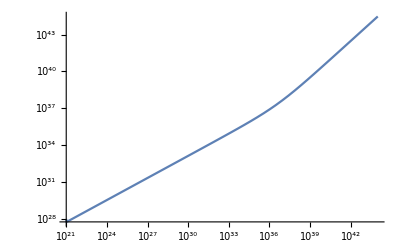

```mathematica
LogLogPlot[Density NS[x],{x,10^21,10^44}]
```

Now, let’s build the function for the whole range as a picewise function taking the R and NR approx,

```mathematica
pw=Piecewise[{{Density NR[x], 0≤ x<10^23}, {Density NS[x],10^23≤ x≤ 10^45},{Density R[x],x>10^45}},None];
dener[p_]:=pw/.x-> p
```

#### Constants

We need to declare the following constants

```mathematica
G = 6.673 10^-8;
Subscript[M, sol]=1.9891 10^33;
c = 2.99792458 10^10;
α=G Subscript[M, sol]/(10^5 c^2);
Subscript[E0, sol]= Subscript[M, sol] c^2;
km3 = (10.0^5)^3;
rmin = 0.001;
rmax = 350;
densup = 7.86;
```

The numerical values of the constants to non-dimensionalise the equations are:

```mathematica
beta[Pc_]:=4 Pi Pc km3 /Subscript[E0, sol];
β =beta[3 10^34];
```

```mathematica
{α,β}
```

{1.47685,0.000210879}

Now we can proceed to do the numerical integration

#### Newton Equations:

We solve first this simple case.

```mathematica
Pc = 3.3 10^34;
Do[
{solution = NDSolve[{p'[r]== If[p[r]>0,-(α dener[p[r]*Pc]*M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solution[[1]];
pressure ad[x_]:=p[x]/.solution[[1]];
Print[rad,"\t", mass ad[rad],"\t",pressure ad[rad]*Pc,"\t", dener[pressure ad[rad]*Pc]/c^2 ]},{rad,16}]
```

```mathematica
dener[pressure ad[5]*Pc]
```

4.69758×10^35

```mathematica
radius=capR-rstep
rstep=0.001;
dener[pressure ad[radius]*Pc]
```

15.

8.18821×10^33

```mathematica
c^2densup
```

7.06422×10^21

```mathematica
While[dener[pressure ad[radius]]/c^2≥densup,
radius=radius+rstep;
Print[radius,"\t",dener[pressure ad[radius]]]]
```

InterpolatingFunction::dmval: Input value {0.000286} lies outside the range of data in the interpolating function. Extrapolation will be used.

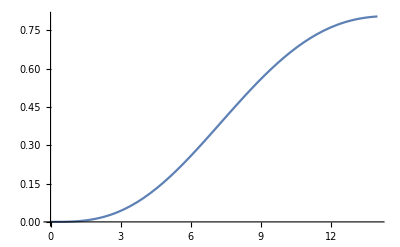

```mathematica
Plot[mass ad[x],{x,0,14}]
```

```mathematica
Plot[dener[pressure ad[x]*Pc],{x,0,14}]
```

InterpolatingFunction::dmval: Input value {0.000286} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

#### TOV Equations:

```mathematica
Pc = 3.3 10^34;
solution = NDSolve[{p'[r]== If[p[r]>0,-(α dener[p[r]*Pc]*M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,14.73},MaxSteps->Infinity]
mass ad[x_]:=M[x]/.solution[[1]];
pressure ad[x_]:=p[x]/.solution[[1]];
```

### TESTS

```mathematica
s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}];
Y[x_]:=y[x]/.s[[1]];
Do[Print[x, " ", Y[x]],{x,10,30,10}]
```

10 0.064349

20 0.191026

30 0.0193018

```mathematica
Do[{s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,fin}];
Y[x_]:=y[x]/.s[[1]];
Print[fin, " ", Y[fin]]},{fin,10,30,10}]
```

10 0.064349

20 0.191026

30 0.0193018